## Mathematica Solution for the Falling Ladder

```mathematica
(* I. Stewart with thanks and credit to S.Ellis *)
```

Consider the angular motion of the falling ladder (a pendulum),  Let β = √(3g/2L)

```mathematica
L=3;  (* 3 meters *)
g = 9.8; β= √(3*g/(2*L))
```

2.21359

Pick a starting angle:

```mathematica
θ0=π/3
```

π/3

Motion when in Contact with wall

Direct numerical solution of the differential equation:

```mathematica
sol1=NDSolve[{θ1''[t]==-Cos[θ1[t]]β^2,θ1[0]==θ0,θ1'[0]==0},θ1,{t,0,5}]
```

{{θ1→InterpolatingFunction[{{0., 5.}}, <>]}}

Direct numerical solution of the differential equation (y-axis in degrees):

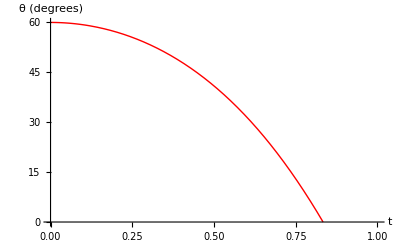

```mathematica
Plot[180/π θ1[t]/.sol1,{t,0,1},PlotRange->{0,180/π π/3},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{"t","θ (degrees)"}]
```

```mathematica
(* Note that in this plot we do not yet account for the change in the solution after the ladder leaves the wall *)
```

Force from wall and floor, divided by Mg

```mathematica
λW[θ_,θ00_]:=3/4 Cos[θ](3 Sin[θ]-2 Sin[θ00])
```

```mathematica
λF[θ_,θ00_]:=1/4(1+9 Sin[θ]^2 -6  Sin[θ] Sin[θ00])
```

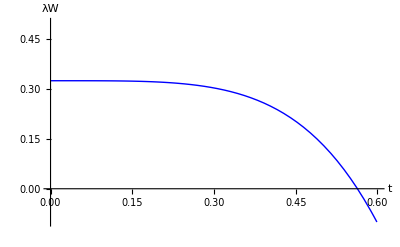

```mathematica
Plot[λW[θ1[t]/.sol1,θ0],{t,0.,0.6},PlotRange->{-.1,.5},PlotStyle->{Thick,Blue},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{t,λW}]
```

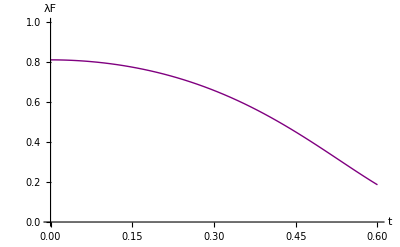

```mathematica
Plot[λF[θ1[t]/.sol1,θ0],{t,0.,0.6},PlotRange->{0,1},PlotStyle->{Thick,Purple},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{t,λF}]
```

Find the time where the force from the wall vanishes (numerical root), call it   t1 .

```mathematica
FindRoot[λW[θ1[t]/.sol1,θ0]==0,{t,0.56,0.57}]
t1 = t /. %;
```

{t→0.563257}

The Angle at this time is what we call θ_c

```mathematica
θc=(θ1[t1]/.sol1)[[1]]      (* the [[1]] gets rid of brackets: {0.61548} *)
```

0.61548

Compare to our analytic solution

```mathematica
ArcSin[2/3 Sin[θ0]]//N
```

0.61548

The horizontal position of the CM when the ladder leaves the wall is

```mathematica
xc=(L*Cos[θ1[t1]/.sol1]/2)[[1]]
```

1.22474

The horizontal motion of the CM as it leaves the wall is

```mathematica
xdotc=(((-L*Sin[θ1[t1]/.sol1]/2))*(D[θ1[t]/.sol1,t]/.t->t1))[[1]]
```

1.45663

8.309,  Problem 2g) Part i) 
Lets make a plot of the solution over the time interval where its valid as requested on the PSet #2

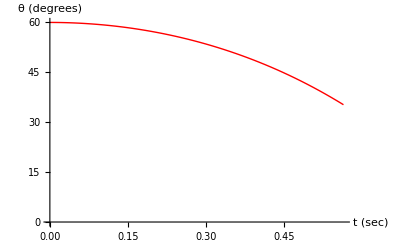

```mathematica
Plot[180/π θ1[t]/.sol1,{t,0,t1},PlotRange->{0,180/π π/3},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{"t (sec)","θ (degrees)"}]
```

To view the motion of our solution so far we express the coordinates of the ladder CM and its ends in terms of the angle

```mathematica
yCM[x_]:=N[L*Sin[x]/2];
xCM[x_]:=N[L*Cos[x]/2];
y[x_]:=N[L*Sin[x]];x[x_]:=N[L*Cos[x]];
```

```mathematica
y[θ1[0.001]/.sol1]
```

{2.59807}

So initially the ladder looks like

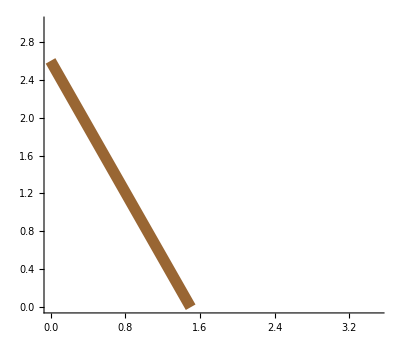

```mathematica
Graphics[{Thickness[0.02],Brown,Line[{{0,y[θ1[t]/.sol1/.t->0.001][[1]]},{x[θ1[t]/.sol1/.t->0.001][[1]],0}}]},Axes->True,PlotRange->{{0,3.5},{0,3}}]
```

Define a "ladder" object for use in the animations

```mathematica
ladder[t_]:=Graphics[{Thickness[0.02],Brown,Line[{{0,y[θ1[t]/.sol1][[1]]},{x[θ1[t]/.sol1][[1]],0}}]},Axes->True,PlotRange->{{0,3.5},{0,3}}]
```

So an animation for the falling ladder while still in contact (what we’ve solved for so far) is

```mathematica
Animate[ladder[t],{t,0,t1},AnimationRunning->False,AnimationRate->0.05]
```

Next Up, Motion when not in Contact

Consider solution of the equation of motion after losing contact with the wall.  Note that the initial condition is set with 
   θ  being equal to θc  found above at the time t1 .

```mathematica
β2=√(12g/L)
```

6.26099

```mathematica
sol2=NDSolve[{θ2'[t]==-β2 √((Sin[θ0]-(1/9)Sin[θ0]^3-Sin[θ2[t]])/(1+3 Cos[θ2[t]]^2)),θ2[t1]==θc},θ2,{t,t1,1.2}]
```

{{θ2→InterpolatingFunction[{{0.563257, 1.2}}, <>]}}

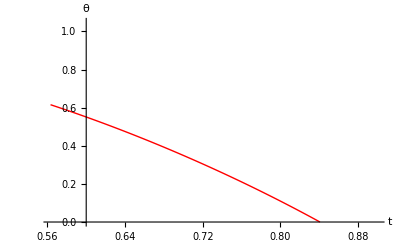

```mathematica
Plot[θ2[t]/.sol2,{t,t1,.9},PlotRange->{0,π/3},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{t,θ}]
```

Determine (numerically) the time when the angle goes to zero and the ladder hits the floor (and we assume that it does not bounce).  Call this t2

```mathematica
FindRoot[(θ2[t]/.sol2)==0,{t,.83,.85}]
t2=t/.%;
```

{t→0.840774}

8.309,  Problem 2g) Part ii) 
Lets make a plot of the solution over the time interval when the ladder is not in contact with the wall, but has not yet hit the floor.

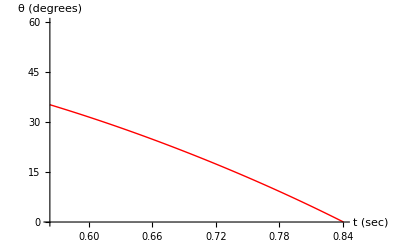

```mathematica
Plot[180/π θ2[t]/.sol2,{t,t1,t2},PlotRange->{0,180/π π/3},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{"t (sec)","θ (degrees)"},AxesOrigin->{t1,0}]
```

Now from the solutions, the force from the floor is

```mathematica
λF2[θ_,θ00_]:=1/((1+3 Cos[θ]^2)^2)(1+3(Sin[θ]-Sin[θ00])^2+3(1-Sin[θ0]^2)+2/3 Sin[θ]Sin[θ00]^3)
```

```mathematica
λF2[.65,θ0]
```

0.263289

The force is always positive

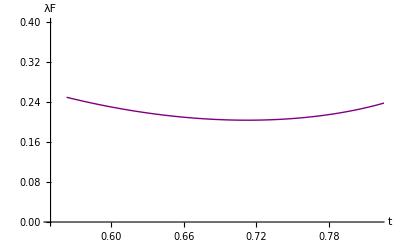

```mathematica
Plot[λF2[θ2[t]/.sol2,θ0],{t,t1,t2},PlotRange->{{.55,.82},{0,0.4}},PlotStyle->{Thick,Purple},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{t,λF}]
```

Now put pieces together. First combine the two solutions for the angle

```mathematica
θ[t_]:=If[t1>t, θ1[t]/.sol1[[1]],If[t2>t,θ2[t]/.sol2[[1]],0]]
```

The derivative of the angle

```mathematica
Dθ[x_]:=If[t1>x, D[θ1[t]/.sol1,t][[1]]/.t->x,If[t2>x,D[θ2[t]/.sol2,t][[1]]/.t->x,0]]
```

Check continuity when we leave the wall (the number differ by the amount we expect):

```mathematica
{θ[t1-10^(-5)],θ[t1+10^(-5)]}
{Dθ[t1-10^(-8)],Dθ[t1+10^(-8)]}
```

{0.615497,0.615463}

{-1.68197,-1.68197}

Check continuity when we hit the floor:

```mathematica
{θ[t2-10^(-5)],θ[t2+10^(-5)]}
{Dθ[t2-10^(-5)],Dθ[t2+10^(-5)]}
```

{0.0000278921,0}

{-2.78919,0}

The derivative of the angle is not continuous since the transition was made abrupt (we assume no bounce).

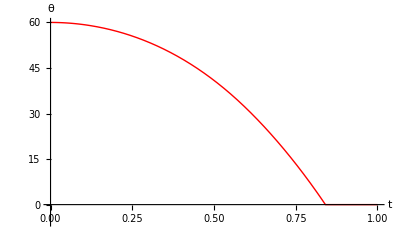

```mathematica
Plot[θ[t]*180/π,{t,0,1},PlotRange->{-0.1*180/π,θ0*180/π},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{t,θ}]
```

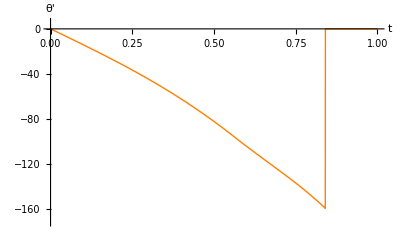

```mathematica
Plot[Dθ[x]*180/π,{x,0,1},PlotRange->{-3*180/π,0.1*180/π},PlotStyle->{Thick,Orange},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{"t","θ'"}]
```

Now construct the force due to the floor for all times:

```mathematica
λFF[t_]:=If[t1>t, λF[θ[t],θ0],λF[θ[t],θ0]]
```

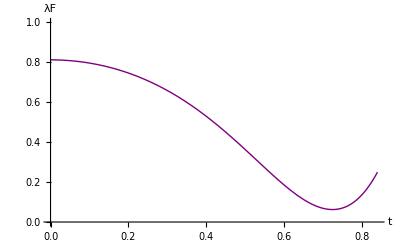

```mathematica
Plot[λFF[t],{t,0,t2},PlotRange->{0,1},PlotStyle->{Thick,Purple},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{t,λF}]
```

Now find the horizontal positions of the 2 ends of the ladder so that we can make an animation.

```mathematica
x2A[t_]:=If[t1>t,0,xc+xdotc*(t-t1)-L* Cos[θ[t]]/2]
```

```mathematica
x2B[t_]:=If[t1>t,x[θ[t]],xc+xdotc*(t-t1)+L Cos[θ[t]]/2]
```

The x coordinate of the left end of the ladder is zero and then moves when the ladder leaves the wall

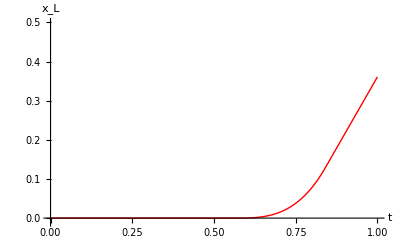

```mathematica
Plot[x2A[t],{t,0,1},PlotRange->{-0.01,0.5},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{"t","x_L"}]
```

The x coordinate of the right end of the ladder is non-zero to start. It is always moving

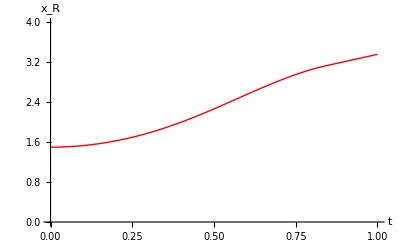

```mathematica
Plot[x2B[t],{t,0,1},PlotRange->{0,4},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"Times",FontSize->18},AxesLabel->{t,Subscript[x, R]}]
```

Make a ladder object (between the 2 ends)

```mathematica
ladder2[t_]:=Graphics[{Thickness[0.02],Brown,Line[{{x2A[t],y[θ[t]]},{x2B[t],0}}]},Axes->True,PlotRange->{{0,3.5},{0,3}}, PlotLabel->"A Falling Ladder"]
```

```mathematica
Animate[ladder2[t],{t,0,1.2},AnimationRunning->False,AnimationRate->0.05]
```

Create a gif animation of the falling ladder

```mathematica
Export["~/mit/courses/8.09/ladder.gif",Table[Show[ladder2[t]],{t,0,1.0,.01}],"DisplayDurations"->0.1]
```

```mathematica
NotebookDirectory[]
```